Making Approximate Systems

```mathematica
enhancedGRN[k1tx_,k1ctx_,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
Module[{null,G1,T1,R1,G1c,T1c,C1,sol,rsys},
rsys={
(* Genelet R1 *)
rxn[G1,G1+T1,k1tx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Genelet C1 *)
rxn[G1c,G1c+T1c,k1ctx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

rxn[C1+R1,null,kc],

conc[G1,1],
conc[G1c,1]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{C1[t],R1[t]}/.sol]

]

enhancedGRNPlot[k1tx_,k1ctx_,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=(
plotter=enhancedGRN[k1tx,k1ctx,tmax];
Plot[plotter,{t,0,100},PlotRange->All,PlotStyle->{{Red},{Green}},PlotLabel->"R1" ])
plot1=Manipulate[enhancedGRNPlot[a,b],{{a,1,"k1tx"},1,500},{{b,250,"k1ctx"},1,500}]
```

Most of these appear to go to s.s. way before 100 s. I' ll just take the lazy approach and take concentrations to be final at 50 s.

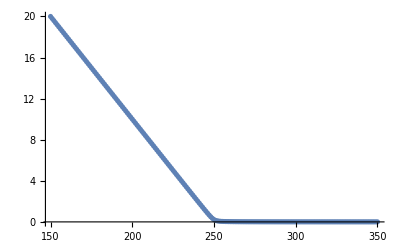

```mathematica
tmax=50;
k1ctx=250;

y=Table[{i,enhancedGRN[i,k1ctx,tmax][[1]][[0]][tmax]},{i,k1ctx-100,k1ctx+100}];
ListPlot[y]
```

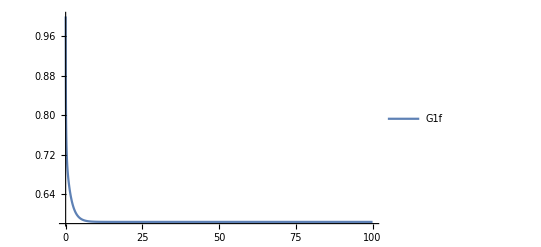

0.58345

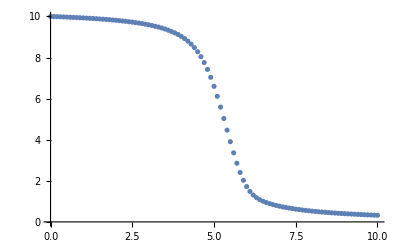

```mathematica
enhancedGRN3[k1tx_,k1ctx_,kf_:400,kr_:125,tmax_:100,kc_:1000,ktl_:1.0,kpd_:1.0,krd_:5.0]:=
Module[{null,G1,T1,R1,G1c,T1c,C1,sol,rsys,G1f,R1G1f},
rsys={
(* Genelet R1 *)
rxn[G1,G1+T1,k1tx],
rxn[T1,T1+R1,ktl],
rxn[T1,null,krd],
rxn[R1,null,kpd],

(* Genelet C1 *)
rxn[G1c,G1c+T1c,k1ctx],
rxn[T1c,T1c+C1,ktl],
rxn[T1c,null,krd],
rxn[C1,null,kpd],

(* Titration *)
rxn[C1+R1,null,kc],

(* "Reporter" Gene *)
revrxn[R1+G1f,R1G1f,kf,kr],

conc[G1,1],
conc[G1c,1],
conc[G1f,10]
};
sol=SimulateRxnsys[rsys,tmax];
Return[{G1f[t]}/.sol]
]

plotter=enhancedGRN2[250,250];
Plot[plotter,{t,0,100},PlotRange->All,PlotLegends->{"G1f"}]
plotter[[1]][[0]][100]

tmax=60;
k1ctx=5;
y=Table[{i,enhancedGRN3[i,k1ctx,1.5,0.05,tmax][[1]][[0]][tmax]},{i,k1ctx-5,k1ctx+5,0.1}];
ListPlot[y]
```

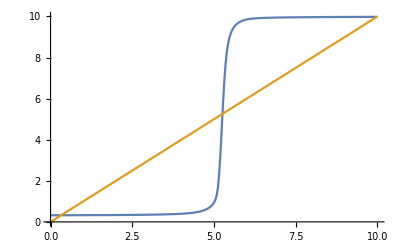

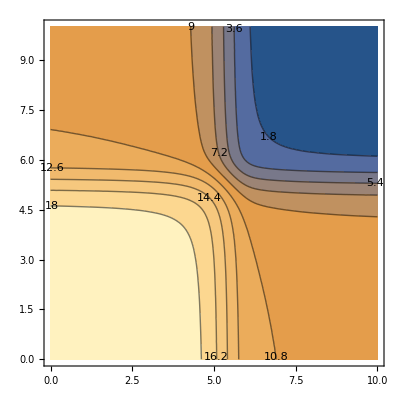

```mathematica
inv=Interpolation[y];
Plot[{inv[inv[x]],x},{x,0,10}]
NAND[x_,y_]:=inv[x]+inv[y]
ContourPlot[NAND[x,y],{x,0,10},{y,0,10},ContourLabels->True,Contours->10]
```

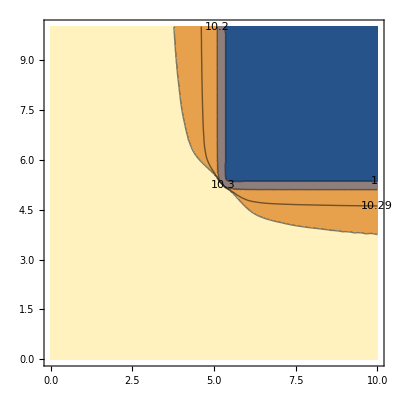

```mathematica
strongNOT[x_]:=inv[inv[inv[x]]]
NAND[x_,y_]:=strongNOT[x]+strongNOT[y]
ContourPlot[NAND[x,y],{x,0,10},{y,0,10},ContourLabels->True,Contours->{1,10.29,10.30,10.2}]
```

Building Composable GRNs

{X+GNY →^1. XGNY ,XGNY →^1. X+GNY ,XGNY →^5. XGNY+TSY ,TSY →^1. TSY+Y ,TSY →^5. null$57431 ,Y →^1. null$57431 ,conc[X,1],conc[GNY,10],Y+GNZ →^1. YGNZ ,YGNZ →^1. Y+GNZ ,YGNZ →^5. YGNZ+TSZ ,TSZ →^1. TSZ+Z ,TSZ →^5. null$57432 ,Z →^1. null$57432 ,conc[Y,0],conc[GNZ,10]}

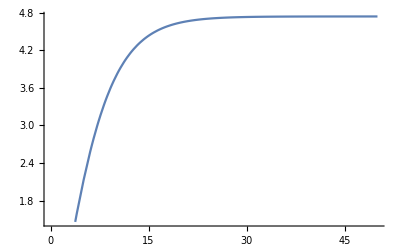

```mathematica
Clear[GRN]
GRN[{IN_,OUT_},init_:{x[0]==0},kON_:1.0,kOFF_:1.0]:=Module[{null,initIN},
(* Gene A1 *)
With[
{c=
Cases[init,v_[0]== b_ ->b]},
initIN=c[[1]]];

out=ToString[OUT];
in=ToString[IN];
gn=Symbol["GN"<>out];
ts=Symbol["TS"<>out];
actGene=Symbol[in<>ToString[gn]];
Seq[
revrxn[IN+gn,actGene,kON,kOFF],
rxn[actGene,actGene+ts,ktx],
rxn[ts,ts+OUT,ktl],
rxn[ts,null,krd],
rxn[OUT,null,kpd],

conc[IN,initIN],
conc[gn,Gtot]

]
]

Clear[Gtot,ktl,krd,kpd,ktx,X,Y,Z]
tmax=50;
Gtot=10;
ktl=kpd=1.0;
krd=5.0;
ktx=5.0;
dummySys={
GRN[{X,Y},{X[0]==1}],
GRN[{Y,Z}]
}

sol=SimulateRxnsys[dummySys,tmax];
plotter={Z[t]}/.sol;
Plot[plotter,{t,0,50}]
```

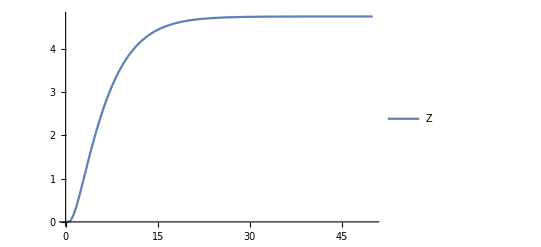

```mathematica
GRNSim[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];

sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol
)


GRNSimPlot[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];
sol=SimulateRxnsys[rsys,time];
plotter=(#[t]&/@watch)/.sol;
Plot[plotter,{t,0,time},PlotRange->All,
PlotLegends->watch]
)

GRNSimPlot[{GRN[{X,Y},{X[0]==1}],GRN[{Y,Z}]},{Z},tmax]
```

Checking for Robustness

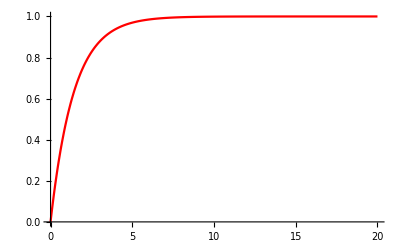

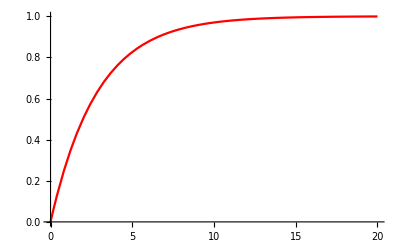

```mathematica
Clear[a,b]
rsys={
rxn[a,b,0.35],
rxn[a,b,0.35],

conc[a,1]
};
tmax=20;
sol=SimulateRxnsys[rsys,tmax];
plotter={b[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{Red}]

Clear[a,b]
rsys={
rxn[a,b,0.35],

conc[a,1]
};
tmax=20;
sol=SimulateRxnsys[rsys,tmax];
plotter={b[t]}/.sol;
Plot[plotter,{t,0,tmax},PlotRange->All,PlotStyle->{Red}]
```

Building Efficient GRNs

```mathematica
Clear[ktx,ktl,kpd,krd,Gtot];
Clear[GRN2];
EnumTF[TF_,gene_,transcript_,ktx_]:=(
boundGene=Symbol[ToString[TF]<>ToString[gene]];
Seq[
revrxn[TF+gene,boundGene,kON,kOFF],
rxn[boundGene,boundGene+transcript,ktx]
]
)


Second[x_]:=x[[2]]

EnumConc[TF_,conc_]:=(
Cases[Tuples[{TF,conc}],{v_,v_[0]==b_}->{v,b}]
)

GRN2[IN_,OUT_,init_]:=(

active=First[#]&/@Select[IN,Second[#]=="ON" &];
repress=First[#]&/@Select[IN,Second[#]=="OFF"&];
With[{nodes= Complement[Join[active,repress],Cases[init,v_[0]== _ -> v]]}, inits=Join[init,(#[0]==0)& /@ nodes ]];
output=ToString[OUT];
gene=Unique["g"<>output];
transcript=Symbol["t"<>output];
Seq[
Function[x,EnumTF[x,gene,transcript,kAct]]/@active,Function[x,EnumTF[x,gene,transcript,kRep]]/@repress,
rxn[gene,gene+transcript,ktx],
rxn[transcript,transcript+OUT,ktl],
rxn[transcript,0,krd],
rxn[OUT,0,kpd],



Function[x,conc[First[x],Second[x]]]/@EnumConc[Join[active,repress],inits],
conc[gene,Gtot]

]
)

Clear[GRNSim2,GRNSimPlot2];
GRNSim2[GRN_,watch_,time_]:=(
rsys=Flatten[GRN];

sol=SimulateRxnsys[rsys/.{kON->0.25,kOFF->0.25,kAct->50.0,kRep->40.0 ,ktx->0.0,ktl->1.0,kpd->1.0,krd->5.0,kc->1000,Gtot->1},time];
(#[t]&/@watch)/.sol
)
GRNSimPlot2[GRN_,watch_,time_]:=(
plotter=GRNSim2[GRN,watch,time];
Plot[plotter,{t,0,time},PlotRange->All,
PlotLegends->watch]
)
```

Proof-of-Concept: NAND gate

```mathematica
Clear[A,B,Z,INT];
NAND1[GRN_,inits_]:=(
inputs=Flatten[GRN];
X=inputs[[1]];
Y=inputs[[2]];
OUT=inputs[[3]];
INT=Symbol[ToString[OUT]<>"INT"];
titr=Symbol[ToString[OUT]<>"T"];
rsys={
{GRN2[{{X,"ON"}},INTX,inits]}/.{kON->0.25,kOFF->0.25,kAct->60.0},
{GRN2[{{Y,"ON"}},INTY,inits]}/.{kON->0.25,kOFF->0.25,kAct->60.0},
rxn[INTX+INTY,INT,kc],
rxn[INT,0,kpd],
conc[titr,5],
rxn[INT+titr,0,kc],

{GRN2[{{INT,"OFF"}},OUT,{INT[0]==0,titr[0]==0}]}/.{kON->2.0,kOFF->1.0,kRep->0.0,ktx->50.0}
}
)

NAND1[{{A,B},Z},{X[0]==0,Y[0]==0}]

tmax=50;
Manipulate[GRNSimPlot2[NAND1[{{A,B},Z},{A[0]==i,B[0]==j}],{A,B,Z,INT},tmax],{{i,1,"X"},0,10},{{j,1,"Y"},0,10}]
```

{{{A+gINTX3815 →^0.25 AgINTX3815 ,AgINTX3815 →^0.25 A+gINTX3815 ,AgINTX3815 →^60. AgINTX3815+tINTX },{},gINTX3815 →^ktx gINTX3815+tINTX ,tINTX →^ktl tINTX+INTX ,tINTX →^krd 0 ,INTX →^kpd 0 ,{conc[A,0]},conc[gINTX3815,Gtot]},{{B+gINTY3816 →^0.25 BgINTY3816 ,BgINTY3816 →^0.25 B+gINTY3816 ,BgINTY3816 →^60. BgINTY3816+tINTY },{},gINTY3816 →^ktx gINTY3816+tINTY ,tINTY →^ktl tINTY+INTY ,tINTY →^krd 0 ,INTY →^kpd 0 ,{conc[B,0]},conc[gINTY3816,Gtot]},INTX+INTY →^kc ZINT ,ZINT →^kpd 0 ,conc[ZT,5],ZINT+ZT →^kc 0 ,{{},{ZINT+gZ3817 →^2. ZINTgZ3817 ,ZINTgZ3817 →^1. ZINT+gZ3817 ,ZINTgZ3817 →^0. ZINTgZ3817+tZ },gZ3817 →^50. gZ3817+tZ ,tZ →^ktl tZ+Z ,tZ →^krd 0 ,Z →^kpd 0 ,{conc[ZINT,0]},conc[gZ3817,Gtot]}}